Define units:

```mathematica
pF=10^-12 s/Ω;
kΩ=10^3 Ω;
s=1/Hz;
```

Photodiode capacitance (DET36A2):

```mathematica
Cjunction=40pF;
```

Plot bandwidth as a function of the terminating resistance:

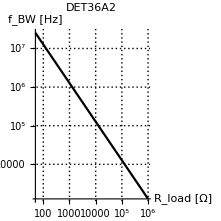

```mathematica
LogLogPlot[
(1./Hz)/(2π Subscript[R, load] Ω 125pF),
{Subscript[R, load],50,10^6},
AxesLabel->{"R_load [Ω]", "f_BW [Hz]"},
PlotRange->Full,
PlotTheme->"GrayColor",
GridLines->Automatic,
AspectRatio->1,
ImageSize->Medium,
PlotLabel->"DET36A2"
]
```

```mathematica
1./(2π 100 Ω 40pF)
```

3.97887×10^7 Hz

```mathematica
(.35)/(50 Ω 40pF)
```

1.75×10^8 Hz